38.0556

5.2

25.

{{t→2.51068}}

2.51068

38.0556 t-2.6 t^2

38.0556-5.2 t

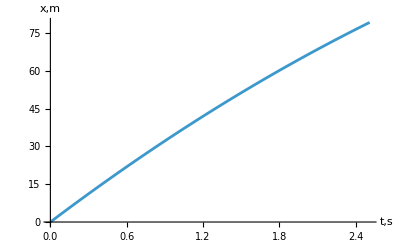

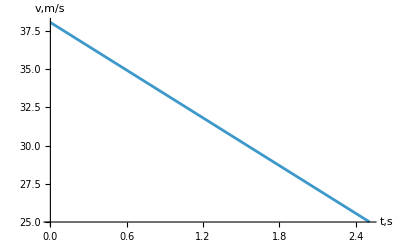

```mathematica
ClearAll["Global`*"]
vp=137*1000/3600//N(*m/s*)
ah=5.2(*m/s^2*)
vd=90*1000/3600//N(*m/s*)
czas=Solve[vp-ah*t==vd,t]
tk=t/.czas[[1]]
x=vp*t-(ah*t^2)/2
v=vp-ah*t(*pochodna*)
Plot[x,{t,0,tk},AxesLabel->{"t,s","x,m"}]
Plot[v,{t,0,tk},AxesLabel->{"t,s","v,m/s"}]
```